```mathematica
Clear[m]
proj=1/2(PauliMatrix[0]+Sum[m[i]*PauliMatrix[i],{i,3}]);
```

```mathematica
$Assumptions=-1<=m[1]<=1&&-1<=m[2]<=1&&-1<=m[3]<=1&&0<=θ<π&&-π<=ϕ<π;

m[1]=Sin[θ]Cos[ϕ];
m[2]=Sin[θ]Sin[ϕ];
m[3]=Cos[θ];

state = proj.{1,1};
norm = Norm[state];
state =state/ norm//FullSimplify
state={ⅇ^(-ⅈ ϕ/2)Cos[θ/2],ⅇ^(ⅈ ϕ/2)Sin[θ/2]};
(*state={Cos[θ/2],ⅇ^(ⅈ ϕ)Sin[θ/2]};*)
state†.state//FullSimplify

Table[(state†.PauliMatrix[i].state//FullSimplify)/.{m[3]^2->1-m[2]^2-m[1]^2}//FullSimplify,{i,3}]
Table[(stateᵀ.PauliMatrix[i].state*//FullSimplify)/.{m[3]^2->1-m[2]^2-m[1]^2}//FullSimplify,{i,3}]
Table[(stateᵀ.PauliMatrix[i].state//FullSimplify)//FullSimplify,{i,3}]
Table[(state†.PauliMatrix[i].state*//FullSimplify)//FullSimplify,{i,3}]
(%*(m[2]+ⅈ m[3])/ⅈ//FullSimplify)/.m[3]^2->1-m[1]^2-m[2]^2//FullSimplify
%/.m[3]^2->1-m[1]^2-m[2]^2//FullSimplify
```

{(1+Cos[θ]+ⅇ^(-ⅈ ϕ) Sin[θ])/(2 √(1+Cos[ϕ] Sin[θ])),(1-Cos[θ]+ⅇ^(ⅈ ϕ) Sin[θ])/(2 √(1+Cos[ϕ] Sin[θ]))}

1

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

{Cos[ϕ] Sin[θ],-Sin[θ] Sin[ϕ],Cos[θ]}

{Sin[θ],0,Cos[θ] Cos[ϕ]-ⅈ Sin[ϕ]}

{Sin[θ],0,Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]}

{Sin[θ] (Cos[θ]-ⅈ Sin[θ] Sin[ϕ]),0,(Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]) (Cos[θ]-ⅈ Sin[θ] Sin[ϕ])}

{Sin[θ] (Cos[θ]-ⅈ Sin[θ] Sin[ϕ]),0,(Cos[θ] Cos[ϕ]+ⅈ Sin[ϕ]) (Cos[θ]-ⅈ Sin[θ] Sin[ϕ])}

```mathematica
state†.state**(state†.state*)*//FullSimplify
%/.m[3]^2->1-m[1]^2-m[2]^2//FullSimplify
```

1/4 (3+Cos[2 θ]+2 Cos[2 ϕ] Sin[θ]^2)

1/4 (3+Cos[2 θ]+2 Cos[2 ϕ] Sin[θ]^2)

```mathematica
state†.state*//FullSimplify
(2 m[2] (m[2]-ⅈ m[3]))/(1+m[1] (2+m[1])+m[2]^2+m[3]^2)/.m[3]^2->1-m[1]^2-m[2]^2//FullSimplify
```

Cos[θ/2]^2+ⅇ^(-2 ⅈ ϕ) Sin[θ/2]^2

(Sin[θ] Sin[ϕ] (-ⅈ Cos[θ]+Sin[θ] Sin[ϕ]))/(1+Cos[ϕ] Sin[θ])

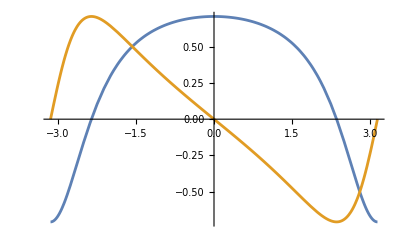

```mathematica
Plot[(ⅇ^(-ⅈ ϕ) (Cos[θ/2]+ⅇ^(ⅈ ϕ) Sin[θ/2])^2 Sin[θ])/(1+Cos[ϕ] Sin[θ])/.θ->π/4//ReIm//Evaluate,{ϕ,-π,π}]
```

```mathematica
state†.state*//FullSimplify
```